## Tests

### Regge cuts study

#### t_proton

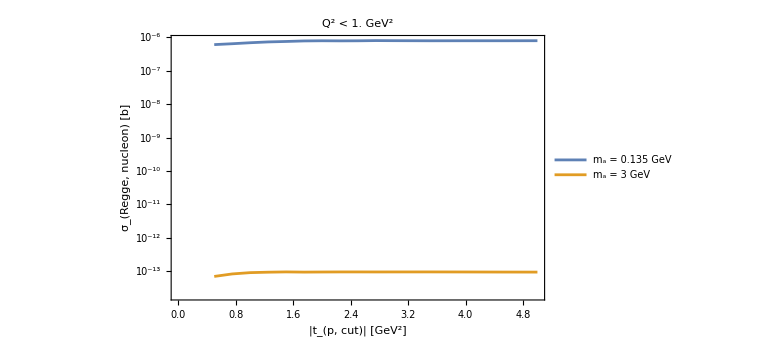

```mathematica
With[{P="π^0",Ep=100.,Ee=10.,ifs1=True,ift2=True,useLogS2Lower=True,useLogT1=True,useLogT2=True,useCosS1=True,Nevents=10^6},
tabbmπ={#,BlockPointsWeightsP[MASS["π^0"],1.,"π^0",Ep,Ee,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,t1thresholdRegge,-#]//Total}&/@{0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.5,4.,4.5,5.};
tabb3={#,BlockPointsWeightsP[3.,1.,"ALP",Ep,Ee,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,t1thresholdRegge,-#]//Total}&/@{0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.5,4.,4.5,5.};
ListLogPlot[{tabbmπ,tabb3},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20],Joined->True,FrameLabel->{"|t_(p, cut)| [GeV^2]","σ_(Regge, nucleon) [b]"},PlotLabel->Style[Row[{"Q^2 < ",Abs[t1thresholdRegge]," GeV^2"}],20,Black],PlotLegends->Placed[Style[Row[{"m_a = ",#," GeV"}],20,Black]&/@{mπval,3},{0.2,0.2}]]
]
```

#### t_electron

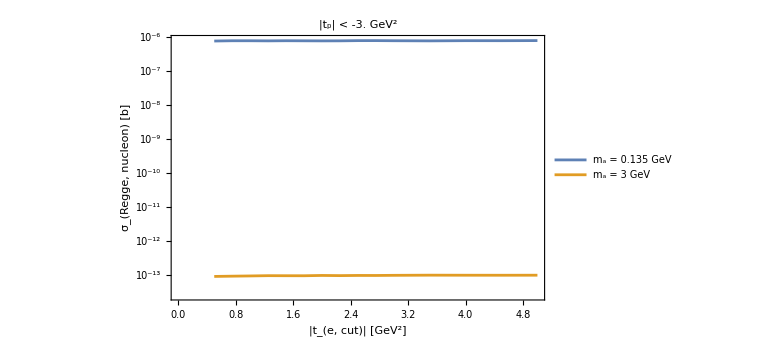

```mathematica
With[{P="π^0",t2thresholdRegge=-3.,Ep=100.,Ee=10.,ifs1=True,ift2=True,useLogS2Lower=True,useLogT1=True,useLogT2=True,useCosS1=True,Nevents=10^6},
tabbmπ={#,BlockPointsWeightsP[MASS["π^0"],1.,"π^0",Ep,Ee,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,-#,t2thresholdRegge]//Total}&/@{0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.5,4.,4.5,5.};
tabb3={#,BlockPointsWeightsP[3.,1.,"ALP",Ep,Ee,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,-#,t2thresholdRegge]//Total}&/@{0.5,0.75,1.,1.25,1.5,1.75,2.,2.25,2.5,2.75,3.,3.5,4.,4.5,5.};
]
ListLogPlot[{tabbmπ,tabb3},ImageSize->Large,Frame->True,FrameStyle->Directive[Thick,Black,20],Joined->True,FrameLabel->{"|t_(e, cut)| [GeV^2]","σ_(Regge, nucleon) [b]"},PlotLabel->Style[Row[{"|t_p| < ",t2thresholdRegge," GeV^2"}],20,Black],PlotLegends->Placed[Style[Row[{"m_a = ",#," GeV"}],20,Black]&/@{mπval,3},{0.2,0.2}]]
```

```mathematica
tabPDFdata[[2]]
```

{2.93013×10^-14,2.55306}

### MC vs analytic

#### Defining block

```mathematica
testMCvsAnalytic[X_,fa_,mX_,Eptest_,Eetest_,Nevents_]:=Block[{ifs1=True,ift2=True,useLogS2Lower=True,useLogT1=True,useLogT2=True,useCosS1=True,tmin,tmax,s2min,s2max,mass=If[X=="ALP",mX,MASS[X]]},
If[MemberQ[{"π^0","η","η'","ALP"},X],
σAn=σPprodAnalytic1[X,mass,fa,Eptest,Eetest];
σAn2=σPprodAnalytic[X,mass,fa,Eptest,Eetest];
σMC=BlockPointsWeightsP[mass,fa,X,Eptest,Eetest,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,t1thresholdRegge,t2thresholdRegge]//Total;
,
σAn=σVprodAnalytic1[X,Eptest,Eetest];
σAn2=σVprodAnalytic2[X,Eptest,Eetest];
σMC=BlockPointsWeightsV[mass,X,Eptest,Eetest,ifs1,ift2,useLogS2Lower,useLogT1,useLogT2,useCosS1,Nevents,t1thresholdRegge,t2thresholdRegge]//Total;
];
tabdσdt1Analytic=tabbt1;
tabdσds2Analytic=tabbs2;
(*Defines pts*)
Print["Cross-sections:"];
tabcomp={{"Semi-analytic, 3D integral",σAn},{"Semi-analytic, 2D + interpolation",σAn2},{"MC",σMC}};
Print[tabcomp];
Print["t_1,min/max - from sampled pool or from analytic bounds:"];
tabcomp2=Join[{{"Approach","(t_(1, min))/GeV^-2","(t_(1, max))/GeV^-2"}},Join[{{"Semi-analytic"},{"MC"}},{t1pmXprod[s,s2minXprod[mp,mX,me,s],me,mp]/.{s->sep[Eptest,Eetest,mp,me]}/.{me->meval,mp->mpval,mX->mass},pts[[All,2]]//MinMax},2]];
Print[tabcomp2];
Print[Row[{"Fraction of zero weights: ", Length[Select[weights,#==0.&]]/Length[weights]//N}]];
(*Creating PDF dσ/d|Subscript[t, 1]|*)
pool1=RandomChoice[weights->pts,Nevents/10//IntegerPart];
inbins={{1,70},{2,100},{3,40}};
{pdfdatas2,pdfdatat1,pdfdatat2}=Table[{#[[1]],σMC*#[[2]]}&/@pdf1Dmaker[pool1,f[[1]],f[[2]]],{f,inbins}];
{pdfs2[x_],pdft1[x_],pdft2[x_]}=Table[If[Min[t[[All,1]]]<=x<=Max[t[[All,1]]],Evaluate[Interpolation[({#[[1]],#[[2]]+10^-90.}&/@t)//Log,InterpolationOrder->1][Log[x]]//Exp],10^-90.],{t,{pdfdatas2,pdfdatat1,pdfdatat2}}];
tabPDFdata={MinMax[pdfdatas2[[All,1]]],MinMax[pdfdatat1[[All,1]]],MinMax[pdfdatat2[[All,1]]]};
{tmin,tmax}=MinMax[Drop[tabPDFdata,1]//Flatten];
dσdt1AnalyticInt[t1_]=Interpolation[tabdσdt1Analytic//Log,InterpolationOrder->1][Log[t1]]//Exp;
nameen=With[{n=ToString[Eptest]<>"×"<>ToString[Eetest]},If[MemberQ[EnergiesConfigurations,n],compactNameConf[n],Row[{"E_p×E_e = ",Eptest," GeV×",Eetest," GeV"}]]];
epilog={Inset[Framed[Style[Row[{"e p → e p ",X,", ",nameen}],22,Black,FontFamily->"Palatino"],FrameStyle->Directive[Black,Thickness[0.9]],Background->White,FrameMargins->Medium],Scaled[{0.22,0.89}]]};
ptt1t2=LogLogPlot[Evaluate[{pdft1[x],pdft2[x],dσdt1AnalyticInt[x]}],{x,tmin,tmax},PlotRange->{{tmin,tmax},{Min[(#[[All,2]]//Max)&/@{pdfdatat1,pdfdatat2}]*4*10^-6,Max[(#[[All,2]]//Max)&/@{pdfdatat1,pdfdatat2}]*4}},FrameLabel->{"|x| [GeV^2]","dσ/d|x| [b/GeV^2]"},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thickness[0.01],Blue,Dashing[0.01]}},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotLegends->Placed[Style[Row[{#}],18,Black,FontFamily->"Palatino"]&/@{"x = Q^2, MC", "x = t_p, MC","x = Q^2, an"},{0.8,0.8}],ImageSize->Large,PlotLabel->Style[nameen,20,Black,FontFamily->"Palatino"],Epilog->epilog]//Quiet;
{pdfdataLogt1,tabdσdLogt1Analytic}=Table[{#[[1]],btofb#[[1]]*#[[2]]}&/@tab,{tab,{pdfdatat1,tabdσdt1Analytic}}];
ptt1forpaper=ListLogLogPlot[Evaluate[{pdfdataLogt1,tabdσdLogt1Analytic}],PlotRange->{tabPDFdata[[2]],(*Max[pdfdataLogt1[[All,2]]]*{10^-3,4}*){10^4.,10^9.}},FrameLabel->{"Q^2 [GeV^2]",Row[{Subscript["Q^2dσ",X],"/dQ^2 [fb/GeV^2]"}]},Joined->True,InterpolationOrder->{0,1},PlotStyle->{{Thick,Blue},{Thick,Darker@Red},{Thickness[0.01],Blue,Dashing[0.01]}},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotLegends->Placed[Style[Row[{#}],18,Black,FontFamily->"Palatino"]&/@{"Monte-Carlo","Analytic"},{0.8,0.8}],ImageSize->Large(*,PlotLabel->Style[nameen,20,Black,FontFamily->"Palatino"]*),FrameTicks->ticksLogXrare,ImagePadding->{{Automatic, Automatic}, {Automatic, Automatic}},Epilog->epilog]//Quiet;
dσds2AnalyticInt[s2_]=Interpolation[tabdσds2Analytic//Log,InterpolationOrder->1][Log[s2]]//Exp;
{s2min,s2max}=tabPDFdata[[1]];
pts2=LogLogPlot[Evaluate[{pdfs2[x],dσds2AnalyticInt[x]}],{x,s2min,s2max},PlotRange->{{s2min,s2max},MinMax[pdfdatas2[[All,2]]]*{10^-6,4}},FrameLabel->{"s_(γ^*) [GeV^2]",Row[{Subscript["dσ",X],"/ds_(γ^*) [b/GeV^2]"}]},PlotStyle->{{Thick,Blue},{Thickness[0.01],Blue,Dashing[0.01]}},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotLegends->Placed[Style[Row[{#}],18,Black,FontFamily->"Palatino"]&/@{"MC", "An"},{0.8,0.8}],ImageSize->Large,PlotLabel->Style[nameen,20,Black,FontFamily->"Palatino"],ImagePadding->{{Automatic, 0.6}, {Automatic, 0.6}}]//Quiet;
pts2forpaper=ListLogLogPlot[Evaluate[Table[{#[[1]],#[[2]]*btofb}&/@tab,{tab,{pdfdatas2,tabdσds2Analytic}}]],Joined->True,PlotRange->{{IntegerPart[s2min],50.},(*Max[pdfdatas2[[All,2]]]*{10^-6,4}*btofb*){10^4.,10^9.}},FrameLabel->{"s_(γ^*) [GeV^2]",Row[{Subscript["dσ",X],"/ds_(γ^*) [fb/GeV^2]"}]},InterpolationOrder->{0,1},PlotStyle->{{Thick,Blue},{Thick,Darker@Red}},Frame->True,FrameStyle->Directive[Thick,Black,22,FontFamily->"Palatino"],PlotLegends->Placed[Style[Row[{#}],18,Black,FontFamily->"Palatino"]&/@{"Monte-Carlo", "Analytic"},{0.8,0.8}],ImageSize->Large(*,PlotLabel->Style[nameen,20,Black,FontFamily->"Palatino"]*),ImagePadding->{{Automatic, Automatic}, {Automatic, Automatic}},FrameTicks->ticksLogX,Epilog->epilog]//Quiet;
Style[Row[{ptt1t2,pts2}],ImageSizeMultipliers->{1,1}]
]
```

#### Examples

Cross-sections:

(Semi-analytic, 3D integral | 3.00743×10^-8
Semi-analytic, 2D + interpolation | 3.02862×10^-8
MC | 3.0336×10^-8)

t_1,min/max - from sampled pool or from analytic bounds:

(Approach | (t_(1, min))/GeV^-2 | (t_(1, max))/GeV^-2
Semi-analytic | -3996.32 | -1.20383×10^-13
MC | -3996.3 | -1.20384×10^-13)

Fraction of zero weights: 0.240205

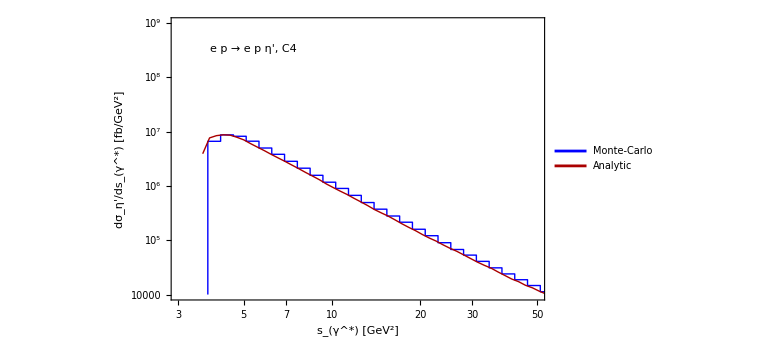
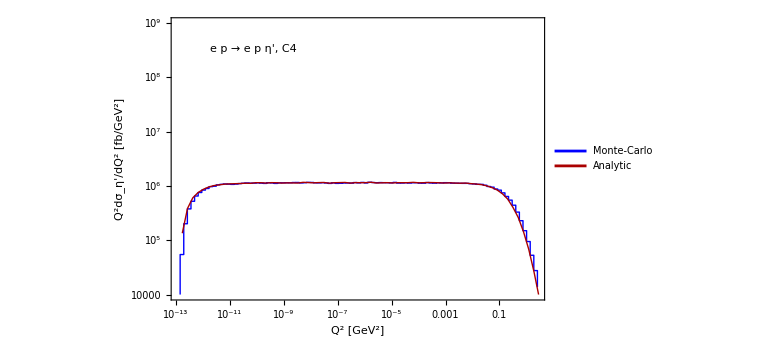

```mathematica
testMCvsAnalytic["η'",1.,MASS["η'"],100,10,2*10^7];
Style[Row[{pts2forpaper,ptt1forpaper}],ImageSizeMultipliers->{1, 1}]
```

Pseudoscalar particle

Cross-sections:

(Semi-analytic, 3D integral | 1.13169×10^-7
Semi-analytic, 2D + interpolation | 1.1255×10^-7
MC | 1.13269×10^-7)

t_1,min/max - from sampled pool or from analytic bounds:

(Approach | (t_(1, min))/GeV^-2 | (t_(1, max))/GeV^-2
Semi-analytic | -3997.71 | -2.86792×10^-14
MC | -3997.7 | -2.86792×10^-14)

Fraction of zero weights: 0.229049

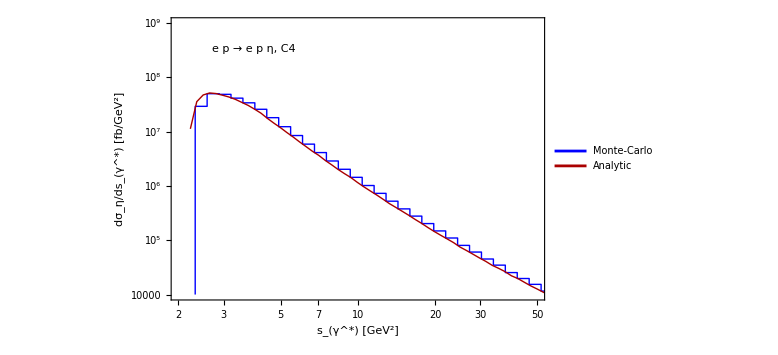
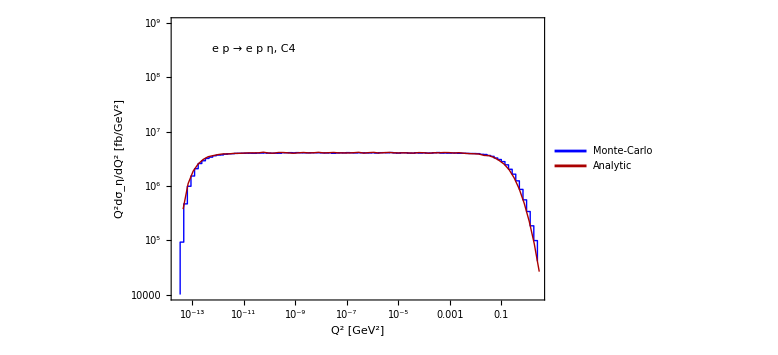

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\MC-vs-analytic-s2.pdf

C:\Users\miksi\Dropbox\Science 2\HNL and scalar phenomenology\ALPs at EIC\plots\MC-vs-analytic-Q2.pdf

```mathematica
testMCvsAnalytic["η",1.,MASS["η"],100,10,5*10^7];
Style[Row[{pts2forpaper,ptt1forpaper}],ImageSizeMultipliers->{1, 1}]
Export[FileNameJoin[{dir["plots"],"MC-vs-analytic-s2.pdf"}],pts2forpaper]
Export[FileNameJoin[{dir["plots"],"MC-vs-analytic-Q2.pdf"}],ptt1forpaper]
```

Vector particle

Cross-sections:

(Semi-analytic, 3D integral | 5.70997×10^-6
Semi-analytic, 2D + interpolation | 3.95776×10^-87
MC | 5.73273×10^-6)

t_1,min/max - from sampled pool or from analytic bounds:

(Approach | (t_(1, min))/GeV^-2 | (t_(1, max))/GeV^-2
Semi-analytic | -3996.98 | -6.89266×10^-14
MC | -3996.98 | -6.89268×10^-14)

Fraction of zero weights: 0.252524

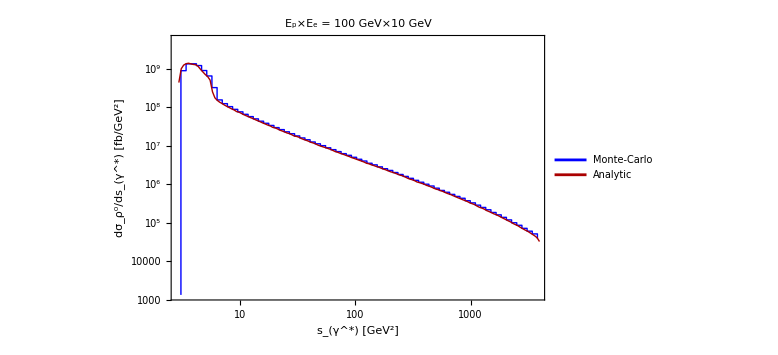
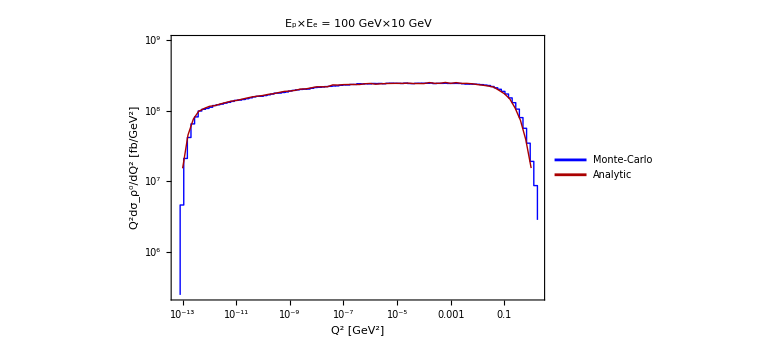

```mathematica
testMCvsAnalytic["ρ^0",1.,MASS["ρ^0"],100,10,5*10^7];
Style[Row[{pts2forpaper,ptt1forpaper}],ImageSizeMultipliers->{1, 1}]
```